## Explore phase transition to a connected graph in ER model Problem 14.2 (and also Section 14.1.3, Random networks)

```mathematica
Clear["Global`*"];
```

```mathematica
𝒟[n_,p_]:=GraphPropertyDistribution[Boole[ConnectedGraphQ[g]],g\[Distributed]BernoulliGraphDistribution[n,p]]
```

```mathematica
prob1[n_,p_]:=NProbability[x==1,x\[Distributed]𝒟[n,p],Method->{"MonteCarlo",PrecisionGoal->1,,AccuracyGoal->1}]
```

```mathematica
pcrit[n_]:=Log[n]/(n-1)
```

```mathematica
{pcrit[1000.],prob1[1000,0.012]}
```

{0.00691467,0.9965}

```mathematica
p1000=ParametricPlot[{p/pcrit[1000],prob1[1000,p]},{p,0.005,0.012},PlotPoints->20,MaxRecursion->0,Mesh->All,MeshStyle->Directive[PointSize[0.03],Red],PlotRange->All];
```

```mathematica
pcrit[100.]
```

0.0465169

```mathematica
p100=ParametricPlot[{p/pcrit[100],prob1[100,p]},{p,0.025,0.07},PlotPoints->30,MaxRecursion->0,Mesh->All,MeshStyle->Directive[PointSize[0.03],Green],PlotRange->All];
```

```mathematica
{pcrit[10.],prob1[10,0.7]}
```

{0.255843,0.999875}

```mathematica
p10=ParametricPlot[{p/pcrit[10],prob1[10,p]},{p,0.07,0.4},PlotPoints->30,MaxRecursion->0,Mesh->All,MeshStyle->Directive[PointSize[0.03],Blue],PlotRange->All];
```

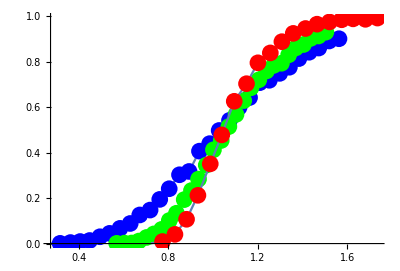

```mathematica
Show[{p10,p100,p1000}]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["ERtrans10.dat",p10[[1,1]]];
*)
```